## Adaptive Step Bisection test!

### Setup

```mathematica
l=0; 
range={11.5,13.};
```

```mathematica
MakeGrid[Δρ1_,Δρ2_,ρ0_,ρinf_]:=Module[{i,grid,lo,hi},
grid={};
i=0;(*here i is playing the role of ρ*)
While[i<ρinf,
lo=.5Δρ2 Tanh[(i-ρ0)/100]+.5Δρ2+Δρ1;(*Subscript[ρ, n]-Subscript[ρ, n-1]*)
i=i+.5Δρ2 Tanh[(i-ρ0)/100]+.5Δρ2+Δρ1;(*ρ, updated*)
hi=.5Δρ2 Tanh[(i-ρ0)/100]+.5Δρ2+Δρ1;(*Subscript[ρ, n+1]-Subscript[ρ, n]*)
grid=Append[grid,{lo,i,hi}];
];
Return[grid]
]
```

```mathematica
Critical[λ_,consts_]:=Module[{H,res,ρs,nn,a,b,rho},
ρs=MakeGrid[consts];
nn=Length[ρs];
a[n_]:=ρs[[n,1]];
b[n_]:=ρs[[n,3]];
rho[n_]:=ρs[[n,2]];
H=SparseArray[{{n_,n_}:>4./(a[n]^2+b[n]^2)-2./rho[n] ⅇ^(-rho[n]/λ)+(l*(l+1))/(rho[n])^2,{n_, m_}/; Abs[n-m] == 1 :> -2./(a[n]^2+b[n]^2)},{nn,nn}, 0.];
H=N[H];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
Bisect[F_,consts_,x0_,val_,xf_,ϵ_]:=Module[{mid,newval,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]]; (*Again, lets you know it's working/progress*)
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,val,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,vam,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
Findlc[F_,consts_,x0_,xf_,ϵ_]:=Module[{val,vah,lnegs,hnegs,res},
Print["****beginning calculation"];
val=F[x0,consts];
res=Bisect[F,consts,x0,val,xf,ϵ];
Return[res]
]
```

```mathematica
DistributeDefinitions[range,Bisect,Critical,MakeGrid,l,CountNegs,Findlc]
```

{MakeGrid}

## Collecting data. Defaults: {0.1, 2, 100, 25000}

### Varying ρ0

```mathematica
ρ0s=Table[i,{i,50,500,50}];
```

```mathematica
DistributeDefinitions[ρ0s];
```

```mathematica
ParallelTable[Timing[Findlc[Critical,{0.1,2,ρ0s[[i]],25000},range[[1]],range[[2]],10^(-6)]],{i,1,10}]
```

****beginning calculation

****beginning calculation

Part::span: 1 ;; {0.1, 2, 200, 25000} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1 ;; {0.1, 2, 50, 25000} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 3 of 1 ;; {0.1, 2, 200, 25000} does not exist.

Part::partw: Part 3 of 1 ;; {0.1, 2, 50, 25000} does not exist.

Part::span: 1 ;; {0.1, 2, 200, 25000} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 3 of 1 ;; {0.1, 2, 200, 25000} does not exist.

SparseArray::valnl: The value specified by the rule {n$_, n$_} :> 4./a$4591[n$]^2 + b$4591[n$]^2 - 2.\ ⅇ^-rho$4591[« 1 »]/11.5/rho$4591[n$] + l\ (l + 1)/rho$4591[n$]^2 should not be a List.

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

Part::span: 1 ;; {0.1, 2, 50, 25000} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 3 of 1 ;; {0.1, 2, 50, 25000} does not exist.

SparseArray::valnl: The value specified by the rule {n$_, n$_} :> 4./a$4504[n$]^2 + b$4504[n$]^2 - 2.\ ⅇ^-rho$4504[« 1 »]/11.5/rho$4504[n$] + l\ (l + 1)/rho$4504[n$]^2 should not be a List.

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

$Aborted

```mathematica
varyr0={{130.27599999999998,{12.47411859035492,0,1}},{131.96099999999998,{12.324426293373108,0,1}},{132.69500000000005,{12.333002924919128,0,1}},{139.621,{12.449331402778625,0,1}},{144.51899999999998,{12.583317399024963,0,1}},{148.856,{12.669992804527283,0,1}},{158.40299999999996,{12.710203051567078,0,1}},{166.765,{12.725611805915833,0,1}},{174.12900000000008,{12.730566382408142,0,1}},{166.063,{12.73152768611908,0,1}}};
```

```mathematica
arraysizesr0=Table[Length[MakeGrid[0.1,2,ρ0s[[i]],25000]],{i,1,10}];
```

```mathematica
timingr0=Table[{arraysizesr0[[i]],varyr0[[i,1]]},{i,1,Length[arraysizes]}]
```

{{11964,130.276},{12050,131.961},{12226,132.695},{12517,139.621},{12901,144.519},{13338,148.856},{13799,158.403},{14270,166.765},{14744,174.129},{15219,166.063}}

```mathematica
r0vals=Table[{ρ0s[[i]],varyr0[[i,2,1]]},{i,1,Length[ρ0s]}]
```

{{50,12.4741},{100,12.3244},{150,12.333},{200,12.4493},{250,12.5833},{300,12.67},{350,12.7102},{400,12.7256},{450,12.7306},{500,12.7315}}

### Varying Δρ1

```mathematica
drhos=Table[0.1*2^-i,{i,0,3}]
```

{0.1,0.05,0.025,0.0125}

```mathematica
DistributeDefinitions[drhos];
```

```mathematica
ParallelTable[Timing[Bisect[Critical,{drhos[[i]],2,100,25000},range[[1]],range[[2]],10^(-6)]],{i,1,4}]
```

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.25

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.2734

Bisecting. Midpoint is 12.332

Bisecting. Midpoint is 12.2617

Bisecting. Midpoint is 12.3262

Bisecting. Midpoint is 12.2559

Bisecting. Midpoint is 12.3232

Bisecting. Midpoint is 12.2529

Bisecting. Midpoint is 12.3247

Bisecting. Midpoint is 12.2515

Bisecting. Midpoint is 12.324

Bisecting. Midpoint is 12.2522

Bisecting. Midpoint is 12.3243

Bisecting. Midpoint is 12.2526

Bisecting. Midpoint is 12.3245

Bisecting. Midpoint is 12.2524

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 11.875

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.0625

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.1563

Bisecting. Midpoint is 12.2734

Bisecting. Midpoint is 12.2031

Bisecting. Midpoint is 12.2852

Bisecting. Midpoint is 12.2266

Bisecting. Midpoint is 12.2793

Bisecting. Midpoint is 12.2383

Bisecting. Midpoint is 12.2764

Bisecting. Midpoint is 12.2441

Bisecting. Midpoint is 12.2778

Bisecting. Midpoint is 12.2412

Bisecting. Midpoint is 12.2786

Bisecting. Midpoint is 12.2397

Bisecting. Midpoint is 12.2782

Bisecting. Midpoint is 12.239

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2386

Bisecting. Midpoint is 12.2779

Bisecting. Midpoint is 12.2388

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.2387

```mathematica
varydrho={{131.75900000000001,{12.324426293373108,0,1}},{136.90600000000006,{12.277984738349915,0,1}},{138.716,{12.252294898033142,0,1}},{138.04499999999985,{12.23869001865387,0,1}}}
```

{{131.759,{12.3244,0,1}},{136.906,{12.278,0,1}},{138.716,{12.2523,0,1}},{138.045,{12.2387,0,1}}}

```mathematica
arraysizesdrho=Table[Length[MakeGrid[drhos[[i]],2,100,25000]],{i,1,4}];
```

```mathematica
timingdrho=Table[{arraysizesdrho[[i]],varydrho[[i,1]]},{i,1,4}]
```

{{12050,131.759},{12358,136.906},{12520,138.716},{12602,138.045}}

```mathematica
drhovals=Table[{drhos[[i]],varydrho[[i,2,1]]},{i,1,4}]
```

{{0.1,12.3244},{0.05,12.278},{0.025,12.2523},{0.0125,12.2387}}

### Varying Δρ2

```mathematica
drhos2=Table[2^i,{i,5,0,-1}]
```

{32,16,8,4,2,1}

```mathematica
DistributeDefinitions[drhos2];
```

```mathematica
ParallelTable[Timing[Bisect[Critical,{0.1,drhos2[[i]],100,25000},range[[1]],range[[2]],10^(-6)]],{i,1,6}]
```

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.25

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Bisecting. Midpoint is 12.625

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.9063

Bisecting. Midpoint is 12.9531

Bisecting. Midpoint is 12.9766

Bisecting. Midpoint is 12.9883

Bisecting. Midpoint is 12.9941

Bisecting. Midpoint is 12.9971

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.9985

Bisecting. Midpoint is 12.9993

Bisecting. Midpoint is 12.9996

Bisecting. Midpoint is 12.9998

Bisecting. Midpoint is 12.9999

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

«2 more identical outputs»

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.9063

Bisecting. Midpoint is 12.9531

Bisecting. Midpoint is 12.9766

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.9883

Bisecting. Midpoint is 12.9941

Bisecting. Midpoint is 12.9971

Bisecting. Midpoint is 12.9985

Bisecting. Midpoint is 12.9993

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.9996

Bisecting. Midpoint is 12.9998

Bisecting. Midpoint is 12.9999

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 12.332

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

«2 more identical outputs»

Bisecting. Midpoint is 12.3379

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.335

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.5313

Bisecting. Midpoint is 12.3364

Bisecting. Midpoint is 12.4844

Bisecting. Midpoint is 12.5078

Bisecting. Midpoint is 12.3372

Bisecting. Midpoint is 12.4961

Bisecting. Midpoint is 12.4902

Bisecting. Midpoint is 12.4873

Bisecting. Midpoint is 12.3375

Bisecting. Midpoint is 12.4888

Bisecting. Midpoint is 12.4895

Bisecting. Midpoint is 12.3377

Bisecting. Midpoint is 12.4891

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.3378

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.3378

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.3378

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.3378

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.3378

Bisecting. Midpoint is 12.3378

Bisecting. Midpoint is 12.3378

«2 more identical outputs»

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.332

Bisecting. Midpoint is 12.3262

Bisecting. Midpoint is 12.3232

Bisecting. Midpoint is 12.3247

Bisecting. Midpoint is 12.324

Bisecting. Midpoint is 12.3243

Bisecting. Midpoint is 12.3245

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

«6 more identical outputs»

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.3906

Bisecting. Midpoint is 12.3672

Bisecting. Midpoint is 12.3555

Bisecting. Midpoint is 12.3613

Bisecting. Midpoint is 12.3643

Bisecting. Midpoint is 12.3657

Bisecting. Midpoint is 12.3665

Bisecting. Midpoint is 12.3668

Bisecting. Midpoint is 12.367

Bisecting. Midpoint is 12.3671

Bisecting. Midpoint is 12.3671

Bisecting. Midpoint is 12.3671

«6 more identical outputs»

```mathematica
varydrho2={{5.600999999999999,{12.999999642372131,0,0}},{9.99899999999991,{12.999999642372131,0,0}},{20.451999999999998,{12.488980174064636,0,1}},{45.45900000000006,{12.337796568870544,0,1}},{103.17900000000009,{12.324426293373108,0,1}},{256.7149999999999,{12.36712920665741,0,1}}}
```

{{5.601,{13.,0,0}},{9.999,{13.,0,0}},{20.452,{12.489,0,1}},{45.459,{12.3378,0,1}},{103.179,{12.3244,0,1}},{256.715,{12.3671,0,1}}}

```mathematica
arraysizesdrho2=Table[Length[MakeGrid[0.1,drhos2[[i]],100,25000]],{i,1,6}];
```

```mathematica
timingdrho2=Table[{arraysizesdrho2[[i]],varydrho2[[i,1]]},{i,1,6}]
```

{{792,5.601},{1577,9.999},{3131,20.452},{6180,45.459},{12050,103.179},{22962,256.715}}

```mathematica
drho2vals=Table[{drhos2[[i]],varydrho2[[i,2,1]]},{i,3,6}](*discard the first two due to no zero*)
```

{{8,12.489},{4,12.3378},{2,12.3244},{1,12.3671}}

### Varying ρinf

```mathematica
ρinfs=Table[25000*2^i,{i,0,3}]
```

{25000,50000,100000,200000}

```mathematica
DistributeDefinitions[ρinfs];
```

```mathematica
ParallelTable[Timing[Bisect[Critical,{0.1,2,100,ρinfs[[i]]},range[[1]],range[[2]],10^(-6)]],{i,1,4}]
```

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.25

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.332

Bisecting. Midpoint is 12.3262

Bisecting. Midpoint is 12.3232

Bisecting. Midpoint is 12.3247

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.324

Bisecting. Midpoint is 12.3243

Bisecting. Midpoint is 12.3245

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

«3 more identical outputs»

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.3086

Bisecting. Midpoint is 12.3145

Bisecting. Midpoint is 12.3174

Bisecting. Midpoint is 12.3188

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.3196

Bisecting. Midpoint is 12.3199

Bisecting. Midpoint is 12.3198

Bisecting. Midpoint is 12.3086

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3145

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3197

«1 more identical outputs»

Bisecting. Midpoint is 12.3174

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3159

Bisecting. Midpoint is 12.3167

Bisecting. Midpoint is 12.317

Bisecting. Midpoint is 12.3172

Bisecting. Midpoint is 12.3173

Bisecting. Midpoint is 12.3173

Bisecting. Midpoint is 12.3173

«6 more identical outputs»

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.3086

Bisecting. Midpoint is 12.3145

Bisecting. Midpoint is 12.3174

Bisecting. Midpoint is 12.3159

Bisecting. Midpoint is 12.3167

Bisecting. Midpoint is 12.3163

Bisecting. Midpoint is 12.3161

Bisecting. Midpoint is 12.3162

Bisecting. Midpoint is 12.3161

Bisecting. Midpoint is 12.3161

Bisecting. Midpoint is 12.3161

«5 more identical outputs»

```mathematica
varyrhoinf={{150.44700000000012,{12.324426293373108,0,1}},{432.9649999999999,{12.319688439369202,0,1}},{1152.1770000000001,{12.317312359809875,0,1}},{5611.465,{12.316122889518738,0,1}}}
```

{{150.447,{12.3244,0,1}},{432.965,{12.3197,0,1}},{1152.18,{12.3173,0,1}},{5611.47,{12.3161,0,1}}}

```mathematica
arraysizesrhoinf=Table[Length[MakeGrid[0.1,2,100,ρinfs[[i]]]],{i,1,4}];
```

```mathematica
timingrhoinfs=Table[{arraysizesrhoinf[[i]],varyrhoinf[[i,1]]},{i,1,4}]
```

{{12050,150.447},{23954,432.965},{47764,1152.18},{95383,5611.47}}

```mathematica
rhoinfvals=Table[{ρinfs[[i]],varyrhoinf[[i,2,1]]},{i,1,4}](*discard the first two due to no zero*)
```

{{25000,12.3244},{50000,12.3197},{100000,12.3173},{200000,12.3161}}

## Analysis

### Timing. Benchmark value: {250000, 743.469}

```mathematica
times=Join[timingdrho,timingdrho2,timingr0]
```

{{12050,131.759},{12358,136.906},{12520,138.716},{12602,138.045},{792,5.601},{1577,9.999},{3131,20.452},{6180,45.459},{12050,103.179},{22962,256.715},{11964,130.276},{12050,131.961},{12226,132.695},{12517,139.621},{12901,144.519},{13338,148.856},{13799,158.403},{14270,166.765},{14744,174.129},{15219,166.063}}

```mathematica
timebenchmark={{250000,743.469}};
```

```mathematica
times=Sort[times]
```

{{792,5.601},{1577,9.999},{3131,20.452},{6180,45.459},{11964,130.276},{12050,103.179},{12050,131.759},{12050,131.961},{12050,150.447},{12226,132.695},{12358,136.906},{12517,139.621},{12520,138.716},{12602,138.045},{12901,144.519},{13338,148.856},{13799,158.403},{14270,166.765},{14744,174.129},{15219,166.063},{22962,256.715},{23954,432.965},{47764,1152.18},{95383,5611.47}}

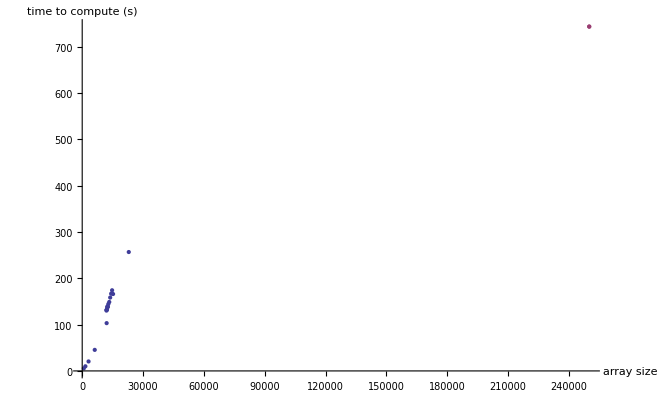

```mathematica
ListPlot[{times,timebenchmark},AxesLabel->{"array size","time to compute (s)"},PlotRange->Full]
```

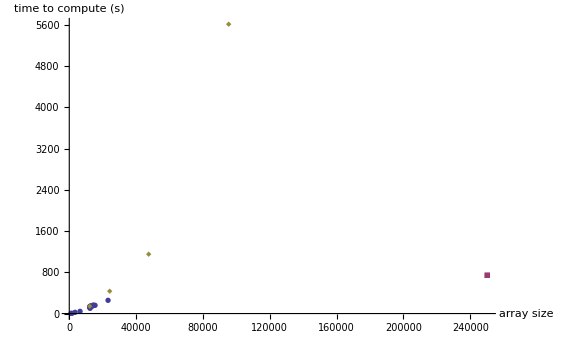

```mathematica
ListPlot[{times,timebenchmark,timingrhoinfs},PlotRange->Full,AxesLabel->{"array size","time to compute (s)"},PlotMarkers->{Automatic,7}]
```

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

### Data. Benchmark value (derived using old code): 12.6913

#### For ρinf:

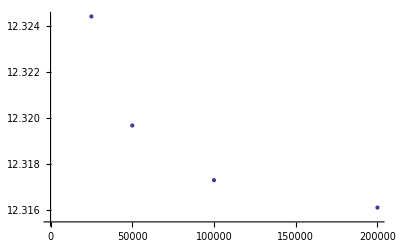

```mathematica
ListPlot[rhoinfvals]
```

This still looks asymtotic, although there are only four points shown. The total movement is not that much -- from 12.324 down to 12.316.

#### For Δρ1

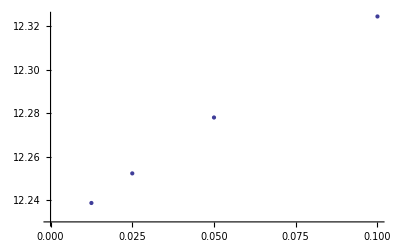

```mathematica
ListPlot[drhovals]
```

At least right here, this looks linear and very significant -- from 12.32 down to 12.24.

#### For Δρ2

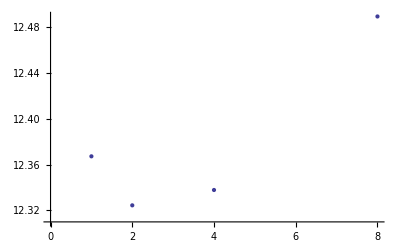

```mathematica
ListPlot[drho2vals]
```

Um...weird. It *increased* at Δρ2 = 1? I wonder if it does that even lower? At a certain point, though, Δρ2 = Δρ1 and we should recover the previous case. Here, at Δρ2 > 8, the bisection started failing, too.

#### For ρ0

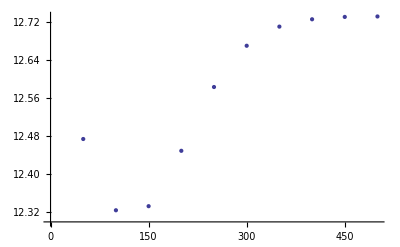

```mathematica
ListPlot[r0vals]
```

That is just really weird.

```mathematica
drhos2=Table[i,{0.1,
```

## More Tests

```mathematica
gridtest=Table[{0.1,i,0.1},{i,0.1,25000,0.1}];
```

```mathematica
Length[gridtest]
```

250000

```mathematica
MakeGrid[size_]:=Module[{i,grid,lo,hi},
grid=gridtest;
Return[grid[[1;;size]]]
]
```

```mathematica
Critical[λ_,consts_]:=Module[{H,res,ρs,nn,a,b,rho},
ρs=MakeGrid[consts];
nn=Length[ρs];
a[n_]:=ρs[[n,1]];
b[n_]:=ρs[[n,3]];
rho[n_]:=ρs[[n,2]];
H=SparseArray[{{n_,n_}->4./(a[n]^2+b[n]^2)-2./rho[n] ⅇ^(-rho[n]/λ)+(l*(l+1))/(rho[n])^2,{n_, m_}/; Abs[n-m] == 1 -> -2./(a[n]^2+b[n]^2)},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-50]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
ρ0s={250000,100000,50000,10000};
```

```mathematica
DistributeDefinitions[MakeGrid,Critical,gridtest];
```

```mathematica
DistributeDefinitions[ρ0s];
```

```mathematica
ParallelTable[Timing[Bisect[Critical,ρ0s[[i]],range[[1]],range[[2]],10^(-6)]],{i,1,4}]
```

Bisecting. Midpoint is 12.25

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

Bisecting. Midpoint is 12.25

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.707

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.7012

Bisecting. Midpoint is 12.7041

Bisecting. Midpoint is 12.7026

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7023

Bisecting. Midpoint is 12.7021

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.702

Bisecting. Midpoint is 12.702

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7019

«1 more identical outputs»

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.7656

Bisecting. Midpoint is 12.7422

Bisecting. Midpoint is 12.7539

Bisecting. Midpoint is 12.7598

Bisecting. Midpoint is 12.7568

Bisecting. Midpoint is 12.7583

Bisecting. Midpoint is 12.7576

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.7572

Bisecting. Midpoint is 12.757

Bisecting. Midpoint is 12.7571

Bisecting. Midpoint is 12.7571

Bisecting. Midpoint is 12.757

Bisecting. Midpoint is 12.757

Bisecting. Midpoint is 12.757

«4 more identical outputs»

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6836

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 12.6924

Bisecting. Midpoint is 12.6909

Bisecting. Midpoint is 12.6917

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6915

Bisecting. Midpoint is 12.6914

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6913

«5 more identical outputs»

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6836

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 12.6924

Bisecting. Midpoint is 12.6938

Bisecting. Midpoint is 12.6946

Bisecting. Midpoint is 12.6949

Bisecting. Midpoint is 12.6951

Bisecting. Midpoint is 12.6952

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6953

«5 more identical outputs»

```mathematica
adaptive={{1764.558,{12.691329598426819,0,1}},{569.9650000000001,{12.695282101631165,0,1}},{374.35599999999977,{12.701913952827454,0,1}},{71.96299999999974,{12.757025122642517,1,2}}}
```

{{1764.56,{12.6913,0,1}},{569.965,{12.6953,0,1}},{374.356,{12.7019,0,1}},{71.963,{12.757,1,2}}}

```mathematica
reg
```

{{730.116,{12.6913,0,1}},{236.7,{12.6953,0,1}},{107.141,{12.7019,0,1}},{16.552,{12.757,0,1}}}

```mathematica
adaptive=Table[{ρ0s[[i]],adaptive[[i,1]]},{i,1,4}]
```

{{250000,1764.56},{100000,569.965},{50000,374.356},{10000,71.963}}

```mathematica
reg=Table[{ρ0s[[i]],reg[[i,1]]},{i,1,4}]
```

{{250000,730.116},{100000,236.7},{50000,107.141},{10000,16.552}}

```mathematica
new=Table[{ρ0s[[i]],new[[i,1]]},{i,1,4}]
```

{{250000,1942.34},{100000,630.197},{50000,406.211},{10000,82.228}}

```mathematica
new2=Table[{ρ0s[[i]],new2[[i,1]]},{i,1,4}]
```

{{250000,1087.83},{100000,362.406},{50000,206.842},{10000,35.786}}

```mathematica
new3=Table[{ρ0s[[i]],new3[[i,1]]},{i,1,4}]
```

{{10000,18.362},{50000,88.094},{100000,232.737},{250000,596.485}}

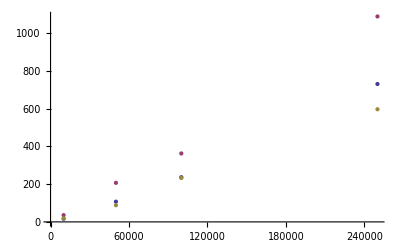

```mathematica
ListPlot[{reg,new2,new3}]
```

```mathematica
Critical[λ_,consts_]:=Module[{H,res,ρs,nn,a,b,rho},
ρs=MakeGrid[consts];
nn=Length[ρs];
a[n_]:=ρs[[n,1]];
b[n_]:=ρs[[n,3]];
rho[n_]:=ρs[[n,2]];
H=SparseArray[{{n_,n_}:>4./(a[n]^2+b[n]^2)-2./rho[n] ⅇ^(-rho[n]/λ)+(l*(l+1))/(rho[n])^2,{n_, m_}/; Abs[n-m] == 1 :> -2./(a[n]^2+b[n]^2)},{nn,nn}, 0.];
H=N[H];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
DistributeDefinitions[Critical];
```

```mathematica
ParallelTable[Timing[Bisect[Critical,ρ0s[[i]],range[[1]],range[[2]],10^(-6)]],{i,1,4}]
```

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.707

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.7012

Bisecting. Midpoint is 12.7041

Bisecting. Midpoint is 12.7026

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7023

Bisecting. Midpoint is 12.7021

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.702

Bisecting. Midpoint is 12.702

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7019

«1 more identical outputs»

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.7656

Bisecting. Midpoint is 12.7422

Bisecting. Midpoint is 12.7539

Bisecting. Midpoint is 12.7598

Bisecting. Midpoint is 12.7568

Bisecting. Midpoint is 12.7583

Bisecting. Midpoint is 12.7576

Bisecting. Midpoint is 12.7572

Bisecting. Midpoint is 12.757

Bisecting. Midpoint is 12.7571

Bisecting. Midpoint is 12.7571

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.757

Bisecting. Midpoint is 12.757

Bisecting. Midpoint is 12.757

«4 more identical outputs»

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6836

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 12.6924

Bisecting. Midpoint is 12.6909

Bisecting. Midpoint is 12.6917

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6915

Bisecting. Midpoint is 12.6914

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6913

«5 more identical outputs»

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6836

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 12.6924

Bisecting. Midpoint is 12.6938

Bisecting. Midpoint is 12.6946

Bisecting. Midpoint is 12.6949

Bisecting. Midpoint is 12.6951

Bisecting. Midpoint is 12.6952

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6953

«5 more identical outputs»

```mathematica
new2={{1087.8270000000002,{12.691329598426819,0,1}},{362.40600000000086,{12.695282101631165,0,1}},{206.84199999999873,{12.701913952827454,0,1}},{35.78600000000006,{12.757025122642517,0,1}}}
```

{{1087.83,{12.6913,0,1}},{362.406,{12.6953,0,1}},{206.842,{12.7019,0,1}},{35.786,{12.757,0,1}}}

```mathematica
new={{1942.3370000000004,{12.691329598426819,0,1}},{630.1969999999992,{12.695282101631165,0,1}},{406.21099999999933,{12.701913952827454,0,1}},{82.22800000000097,{12.757025122642517,1,2}}}
```

{{1942.34,{12.6913,0,1}},{630.197,{12.6953,0,1}},{406.211,{12.7019,0,1}},{82.228,{12.757,1,2}}}

```mathematica
ρs=MakeGrid[250000];
nn=Length[ρs];
a[n_]:=ρs[[n,1]];
b[n_]:=ρs[[n,3]];
rho[n_]:=ρs[[n,2]];
H=SparseArray[{{n_,n_}:>4./(a[n]^2+b[n]^2)-2./rho[n] ⅇ^(-rho[n]/λ)+(l*(l+1))/(rho[n])^2,{n_, m_}/; Abs[n-m] == 1 :> -2./(a[n]^2+b[n]^2)},{nn,nn}, 0.];
```

```mathematica
Timing[Eigenvalues[H,-25]]
```

{7.473,{9.49388×10^-6,8.73358×10^-6,8.00497×10^-6,7.30803×10^-6,6.64277×10^-6,6.00919×10^-6,5.40729×10^-6,4.83707×10^-6,4.29853×10^-6,3.79167×10^-6,3.31648×10^-6,2.87298×10^-6,2.46116×10^-6,2.08102×10^-6,1.73255×10^-6,1.41577×10^-6,1.13068×10^-6,8.77266×10^-7,6.55545×10^-7,4.65523×10^-7,3.07217×10^-7,1.80678×10^-7,8.60595×10^-8,-2.96814×10^-8,2.40956×10^-8}}

```mathematica
λ=12.7;
```

```mathematica
ρs=MakeGrid[250000];
nn=Length[ρs];
```

```mathematica
Timing[SparseArray[{{n_,n_}:>4./(a[n]^2+b[n]^2)-2./rho[n] ⅇ^(-rho[n]/λ)+(l*(l+1))/(rho[n])^2,{n_, m_}/; Abs[n-m] == 1 :> -2./(a[n]^2+b[n]^2)},{nn,nn}, 0.]]
```

{15.35,SparseArray[<749998>,{250000,250000}]}

```mathematica
22*2*(%268[[1]]-%240[[1]])
```

347.952

```mathematica
new2[[1,2]]-reg[[1,2]]
```

357.711

```mathematica
Timing[SparseArray[{{n_,n_}:>4./(a[n]^2+b[n]^2)-2./rho[n] ⅇ^(-rho[n]/λ)+(l*(l+1))/(rho[n])^2,{n_, m_}/; Abs[n-m] == 1 :> -2./(a[n]^2+b[n]^2)},{nn,nn}, 0.]]
```

{0.062,SparseArray[<2998>,{1000,1000}]}

```mathematica
Bisect[F_,consts_,x0_,val_,xf_,ϵ_]:=Module[{mid,newval,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]]; (*Again, lets you know it's working/progress*)
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,val,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,vam,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
Findlc[F_,consts_,x0_,xf_,ϵ_]:=Module[{val,vah,lnegs,hnegs,res},
Print["****beginning calculation"];
val=F[x0,consts];
res=Bisect[F,consts,x0,val,xf,ϵ];
Return[res]
]
```

```mathematica
DistributeDefinitions[Bisect,Findlc]
```

{Findlc}

```mathematica
ρ0s=ListRandomize[ρ0s];
```

```mathematica
DistributeDefinitions[ρ0s]
```

{ρ0s}

```mathematica
ParallelTable[Timing[Findlc[Critical,ρ0s[[i]],range[[1]],range[[2]],10^(-6)]],{i,1,4}]
```

****beginning calculation

****beginning calculation

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6836

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.6924

Bisecting. Midpoint is 12.6938

Bisecting. Midpoint is 12.6946

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.6949

Bisecting. Midpoint is 12.6951

Bisecting. Midpoint is 12.6952

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6953

«4 more identical outputs»

Bisecting. Midpoint is 12.6836

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.6895

****beginning calculation

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.7656

Bisecting. Midpoint is 12.7422

Bisecting. Midpoint is 12.7539

Bisecting. Midpoint is 12.7598

Bisecting. Midpoint is 12.7568

Bisecting. Midpoint is 12.7583

Bisecting. Midpoint is 12.7576

Bisecting. Midpoint is 12.7572

Bisecting. Midpoint is 12.757

Bisecting. Midpoint is 12.7571

Bisecting. Midpoint is 12.7571

Bisecting. Midpoint is 12.757

Bisecting. Midpoint is 12.757

Bisecting. Midpoint is 12.757

«4 more identical outputs»

Bisecting. Midpoint is 12.6924

Bisecting. Midpoint is 12.6909

Bisecting. Midpoint is 12.6917

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6915

Bisecting. Midpoint is 12.6914

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 12.6913

«5 more identical outputs»

****beginning calculation

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.707

Bisecting. Midpoint is 12.7012

Bisecting. Midpoint is 12.7041

Bisecting. Midpoint is 12.7026

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7023

Bisecting. Midpoint is 12.7021

Bisecting. Midpoint is 12.702

Bisecting. Midpoint is 12.702

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7019

Bisecting. Midpoint is 12.7019

«4 more identical outputs»

```mathematica
new3={{596.4850000000006,{12.691329598426819,0,1}},{88.09400000000096,{12.701913952827454,0,1}},{232.73699999999917,{12.695282101631165,0,1}},{18.36200000000099,{12.757025122642517,0,1}}}
```

{{596.485,{12.6913,0,1}},{88.094,{12.7019,0,1}},{232.737,{12.6953,0,1}},{18.362,{12.757,0,1}}}

```mathematica
new3=Sort[new3]
```

{{18.362,{12.757,0,1}},{88.094,{12.7019,0,1}},{232.737,{12.6953,0,1}},{596.485,{12.6913,0,1}}}

```mathematica
ρ0s=Sort[ρ0s]
```

{10000,50000,100000,250000}